```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data.xlsx"];
```

```mathematica
plot1=Transpose[{data[[1]][[2;;11,2]],data[[1]][[2;;11,11]]}]
```

{{300.589,0.370906},{308.638,0.439788},{320.345,0.672655},{329.37,0.982505},{339.37,1.37844},{348.15,1.92007},{361.077,2.74052},{367.906,3.42057},{377.906,4.50515},{387.418,6.11626}}

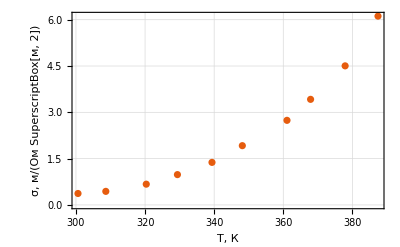

```mathematica
graph1=ListPlot[plot1,PlotTheme->"Scientific",FrameLabel->{"T, К","σ, (:043c)/(:041e:043c SuperscriptBox[:043c, 2])"},GridLines->Automatic]
```

```mathematica
Export["graph1.pdf",graph1]
```

graph1.pdf

```mathematica
plot2=Transpose[{data[[1]][[2;;11,10]],data[[1]][[2;;11,12]]}]
```

{{0.0033268,-0.991808},{0.00324004,-0.821462},{0.00312163,-0.396523},{0.0030361,-0.0176497},{0.00294664,0.320952},{0.00287233,0.652363},{0.00276949,1.00815},{0.00271808,1.22981},{0.00264616,1.50522},{0.00258119,1.81095}}

```mathematica
graph2Fit=LinearModelFit[plot2,x,x]
```

FittedModel[11.6792-3844.78 x]

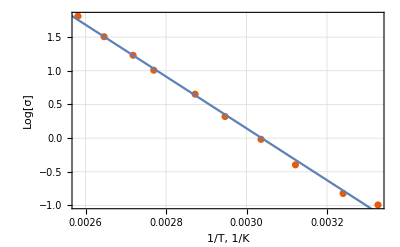

```mathematica
graph2=Show[ListPlot[plot2,PlotTheme->"Scientific",FrameLabel->{"1/T, 1/K", "Log[σ]"},GridLines->Automatic,PlotRange->Full],Plot[graph2Fit["BestFit"],{x,0,1}]]
```

```mathematica
Export["graph2.pdf",graph2]
```

graph2.pdf

```mathematica
k=graph2Fit["BestFitParameters"][[2]]
```

-3844.78

```mathematica
UnitConvert[k*(2Quantity[1,"BoltzmannConstant"])*Quantity[1,"Kelvins"],"Electronvolts"]
```

-0.662635 eV